```mathematica
Mean[Select[StandardDeviation/@Transpose[reconstructed],#>0.&]]
```

57917.4

```mathematica
x=RandomChoice[{0.9,0.1}->{0,1},Length[personalityNames]]
```

{1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,1,1,0,0,1,0,0,0,0,0,0,0,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,1,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,0,1,0,0,0,0,1,0,0,0,0,0,0,0,0,0,0,1,0,0,0,0,0,0,0,1,0,1,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,1,0,0}

```mathematica
x=RandomInteger[{0,1},Length[personalityNames]]
```

{0,0,1,0,0,1,1,1,0,1,0,1,0,1,1,0,1,1,1,1,1,0,0,1,0,1,0,1,0,0,0,1,1,1,1,1,0,1,0,1,0,0,0,1,1,1,1,1,0,0,0,1,1,0,1,0,1,0,0,1,0,0,0,0,0,0,0,0,0,0,0,1,0,0,0,1,1,1,0,0,0,0,0,0,0,1,0,0,0,0,1,0,1,1,1,0,1,1,0,0,0,1,0,0,0,0,1,1,1,1,1,1,1,0,0,0,0,0,1,1,0,0,0,1,0,0,0,0,1,1,1,1,0,1,0,0,0,1,0,1,0,1,1,0,0,0,1,0,1,0,0,1,0,1,1,0,0,1,0,0,1,1,1,1,1,0,0,1,1,0,1,1,1,1,1,0,0,1,0}

```mathematica
allBasisVectors=Transpose[standardized*x];
projected=standardized.allBasisVectors;
reconstructed=projected.Transpose[allBasisVectors]/(57917.4*Total[x]/179.);
```

```mathematica
Mean[StandardDeviation/@Transpose[reconstructed]]
```

0.964423

Things to do:

1. Try to recompute with uncensored model & dark personalities. Generally add more.
2. Finish the importance calc (in a loop), plot the decreasing importance. Sample a bunch of random decreasing importances for random sample of personalities, plot them with whiskers alongside with the best personality order
3. Try to do all samples of len=2, verify if the best one is {137,94}
4. Try to do the same using variance explained instead of error
5. Try to find the nearest personalities to the first principal components, by using:
     - Cosine Similarity (try to do it for both positive and negative values of vector)
6. Change #5 it into loop and automate first 30 - 50 -100 - 150 components
7. Think of another way of picking the order. For example: Look it up, how to find the most “orthogonal” vector to a list of vectors.
8. For “bad” personalities: find out how many dimensions of linear dimension reduction are necessary to tell bad personalities apart from the rest (it can be different vectors from pca or original personalities. (some form of linear regression). Pick 3 most important ones and plot all the personalities in 3D along with bad ones, alongside with the volume of “BAD” given my linear classifier.
OR use SVM and highlight boundary in original PCA 3d plot.

```mathematica
standardized[[10]].Transpose[eigenvectors].Inverse[eigenvectors.Transpose[eigenvectors]].eigenvectors-standardized[[10]]
```

```mathematica
standardized=Transpose[Standardize/@Transpose[allPersMeanOfDiff[[All,18]]]];

(*reconstructErrorPersonalitiesOld[persIndices_]:=Block[
{basisVectors,projected,reconstructed},
basisVectors=Transpose[standardized[[persIndices]]];
projected=standardized.basisVectors;
reconstructed=Standardize/@(projected.Transpose[basisVectors]);
Mean[Flatten[(standardized-reconstructed)^2]]
]*)
```

```mathematica
(*reconstructErrorPersonalities[persIndices_]:=Block[
{basisVectors,projected,reconstructed},
basisVectors=Transpose[standardized[[persIndices]]];
projected=standardized.basisVectors;
reconstructed=Transpose[Normalize/@Transpose[projected.Transpose[basisVectors]]];
Mean[Flatten[(standardized-reconstructed)^2]]
]*)
```

```mathematica
reconstructErrorGivenBasis[basisVectors_]:=Block[
{projected,reconstructed},
reconstructed=standardized.Transpose[basisVectors].Inverse[basisVectors.Transpose[basisVectors]].basisVectors;
Mean[Flatten[(standardized-reconstructed)^2]]
]
```

```mathematica
ClearAll[reconstructErrorPersonalities];
reconstructErrorPersonalities[persIndices_]:=reconstructErrorPersonalities[persIndices]=Block[
{basisVectors,projected,reconstructed},
basisVectors=standardized[[persIndices]];
reconstructErrorGivenBasis[basisVectors]
]
```

```mathematica
(*Function to find the next best personality*)
findNextBestPersonality[currentBest_]:=Module[
{errors,bestIndex,possiblePositions},
possiblePositions=DeleteCases[Range[179],Apply[Alternatives,currentBest]];errors={#,reconstructErrorPersonalities[Append[currentBest,#]]}&/@possiblePositions;
(*bestIndex=PositionSmallest[errors,1][[1,1]];*)
(*{bestIndex,errors[[bestIndex]]}*)
errors[[First@PositionSmallest[errors,1,Order[#1[[2]],#2[[2]]]&]]][[1]]
]

(*Iteratively find the top N personalities*)
findTopPersonalities[n_]:=Module[{topPersonalities={},nextBest,i},For[i=1,i<=n,i++,nextBest=findNextBestPersonality[topPersonalities];
AppendTo[topPersonalities,nextBest[[1]]];
Print["Added personality ",nextBest[[1]]," with error ",nextBest[[2]]];];
topPersonalities]

topPersonalities=findTopPersonalities[178];

(*Calculate errors for all personalities using the top 5*)
errors=reconstructErrorPersonalities[topPersonalities[[;;#]]]&/@Range[178];
```

Added personality 104 with error 0.895881

Added personality 58 with error 0.805787

Added personality 74 with error 0.73241

Added personality 160 with error 0.676585

Added personality 102 with error 0.625778

Added personality 8 with error 0.578316

Added personality 108 with error 0.537735

Added personality 170 with error 0.506779

Added personality 35 with error 0.480934

Added personality 52 with error 0.457225

Added personality 53 with error 0.43659

Added personality 122 with error 0.417918

Added personality 143 with error 0.400639

Added personality 109 with error 0.384256

Added personality 92 with error 0.367891

Added personality 96 with error 0.352559

Added personality 84 with error 0.339155

Added personality 127 with error 0.326738

Added personality 124 with error 0.315212

Added personality 43 with error 0.303884

Added personality 20 with error 0.293728

Added personality 62 with error 0.284383

Added personality 25 with error 0.27533

Added personality 75 with error 0.266459

Added personality 78 with error 0.258175

Added personality 178 with error 0.25021

Added personality 164 with error 0.242377

Added personality 76 with error 0.234939

Added personality 72 with error 0.228358

Added personality 22 with error 0.222054

Added personality 163 with error 0.216137

Added personality 81 with error 0.210263

Added personality 87 with error 0.204918

Added personality 101 with error 0.199894

Added personality 18 with error 0.194879

Added personality 79 with error 0.189966

Added personality 24 with error 0.185122

Added personality 147 with error 0.18048

Added personality 32 with error 0.176149

Added personality 60 with error 0.171843

Added personality 17 with error 0.167641

Added personality 152 with error 0.163622

Added personality 90 with error 0.159675

Added personality 23 with error 0.155834

Added personality 44 with error 0.152127

Added personality 106 with error 0.148494

Added personality 46 with error 0.144934

Added personality 14 with error 0.141429

Added personality 83 with error 0.138038

Added personality 112 with error 0.134716

Added personality 150 with error 0.131517

Added personality 140 with error 0.128349

Added personality 15 with error 0.125233

Added personality 153 with error 0.122204

Added personality 151 with error 0.119233

Added personality 48 with error 0.116375

Added personality 77 with error 0.113522

Added personality 57 with error 0.110872

Added personality 158 with error 0.108309

Added personality 42 with error 0.105801

Added personality 40 with error 0.103325

Added personality 111 with error 0.100944

Added personality 13 with error 0.0985905

Added personality 139 with error 0.0962886

Added personality 93 with error 0.0940452

Added personality 174 with error 0.0918301

Added personality 132 with error 0.089644

Added personality 38 with error 0.0875057

Added personality 161 with error 0.0854415

Added personality 6 with error 0.083402

Added personality 41 with error 0.0813688

Added personality 98 with error 0.0794446

Added personality 173 with error 0.0775809

Added personality 171 with error 0.0757415

Added personality 66 with error 0.0739135

Added personality 37 with error 0.0720942

Added personality 136 with error 0.0703728

Added personality 118 with error 0.0687123

Added personality 134 with error 0.0670834

Added personality 4 with error 0.0654801

Added personality 71 with error 0.0638977

Added personality 97 with error 0.0623778

Added personality 141 with error 0.0608843

Added personality 89 with error 0.0594239

Added personality 59 with error 0.0579719

Added personality 165 with error 0.0565471

Added personality 168 with error 0.0551811

Added personality 64 with error 0.053861

Added personality 1 with error 0.052542

Added personality 70 with error 0.0512403

Added personality 177 with error 0.049948

Added personality 73 with error 0.0486835

Added personality 156 with error 0.047455

Added personality 129 with error 0.0462537

Added personality 99 with error 0.0450817

Added personality 69 with error 0.0439321

Added personality 30 with error 0.0427865

Added personality 61 with error 0.0416706

Added personality 65 with error 0.0405647

Added personality 155 with error 0.0394782

Added personality 27 with error 0.0384021

Added personality 107 with error 0.0373433

Added personality 16 with error 0.0363502

Added personality 12 with error 0.0353608

Added personality 169 with error 0.0344037

Added personality 167 with error 0.0334662

Added personality 121 with error 0.0325627

Added personality 63 with error 0.0316634

Added personality 128 with error 0.0308021

Added personality 117 with error 0.0299702

Added personality 19 with error 0.0291424

Added personality 115 with error 0.0283347

Added personality 144 with error 0.0275558

Added personality 135 with error 0.0267871

Added personality 21 with error 0.0260317

Added personality 148 with error 0.0252838

Added personality 130 with error 0.0245457

Added personality 28 with error 0.0238104

Added personality 9 with error 0.0230996

Added personality 125 with error 0.0224162

Added personality 80 with error 0.0217401

Added personality 33 with error 0.0210668

Added personality 126 with error 0.0204148

Added personality 110 with error 0.01977

Added personality 175 with error 0.0191385

Added personality 120 with error 0.0185182

Added personality 68 with error 0.0179014

Added personality 146 with error 0.0172929

Added personality 67 with error 0.0167012

Added personality 113 with error 0.0161151

Added personality 145 with error 0.0155402

Added personality 49 with error 0.0149799

Added personality 133 with error 0.014432

Added personality 131 with error 0.0138928

Added personality 54 with error 0.0133604

Added personality 10 with error 0.0128296

Added personality 119 with error 0.0123335

Added personality 94 with error 0.0118403

Added personality 123 with error 0.0113542

Added personality 88 with error 0.0108753

Added personality 138 with error 0.0104146

Added personality 50 with error 0.00996156

Added personality 3 with error 0.00952544

Added personality 162 with error 0.00909556

Added personality 154 with error 0.00867791

Added personality 86 with error 0.00826431

Added personality 34 with error 0.0078661

Added personality 149 with error 0.00747649

Added personality 45 with error 0.00709012

Added personality 176 with error 0.006706

Added personality 95 with error 0.00633694

Added personality 91 with error 0.00598545

Added personality 105 with error 0.00564782

Added personality 51 with error 0.00531781

Added personality 5 with error 0.00499649

Added personality 31 with error 0.00467865

Added personality 85 with error 0.00437467

Added personality 142 with error 0.00407851

Added personality 29 with error 0.00378233

Added personality 157 with error 0.00349875

Added personality 159 with error 0.00322382

Added personality 26 with error 0.00296135

Added personality 116 with error 0.00270199

Added personality 179 with error 0.00244376

Added personality 172 with error 0.00219312

Added personality 39 with error 0.00196453

Added personality 36 with error 0.00173594

Added personality 166 with error 0.00151064

Added personality 47 with error 0.00131792

Added personality 56 with error 0.00112884

Added personality 7 with error 0.000947183

Added personality 2 with error 0.000769383

Added personality 103 with error 0.000607182

Added personality 137 with error 0.000451155

Added personality 55 with error 0.000301094

Added personality 11 with error 0.000183185

Added personality 114 with error 0.0000820276

Added personality 82 with error 7.49836×10^-25

```mathematica
(*Create a list of {index,error} pairs*)
indexedErrors=Thread[{topPersonalities,errors}];

(*Sort the pairs by error (ascending order)*)
sortedIndexedErrors=SortBy[indexedErrors,Last];
```

```mathematica
generateRandomSamples[n_]:=Module[{randomOrders,randomErrors},randomOrders=Table[RandomSample[Range[179],178],{n}];
randomErrors=Table[MapIndexed[{#2[[1]],reconstructErrorPersonalities[randomOrder[[1;;#2[[1]]]]]}&,randomOrder],{randomOrder,randomOrders}];
randomErrors]

numRandomSamples=3;  
randomSamples=generateRandomSamples[numRandomSamples];
```

```mathematica
allEigenVectors=Transpose[PrincipalComponents[Transpose[standardized]]];
pcaEigenvectorsErrors=reconstructErrorGivenBasis[allEigenVectors[[;;#]]]&/@Range[178];
```

```mathematica
ListPlot[
{randomSamples[[1]],
randomSamples[[2]],
randomSamples[[3]],
Callout[#2, personalityNames[[#1]]]&@@@indexedErrors,
pcaEigenvectorsErrors
}, 
PlotLegends->{"Original personalities\nin random order 1","Original personalities\nin random order 2","Original personalities\nin random order 3", "Original personalities\nin greedily\noptimized order\n(more interpretable)","PCA eigenvectors\n(less interpretable)"},
PlotLabel->"Re-Construction Error with different linear basis-es",
ImageSize->1020,PlotRange->{{-10,100},Full}]
```

-Graphics-

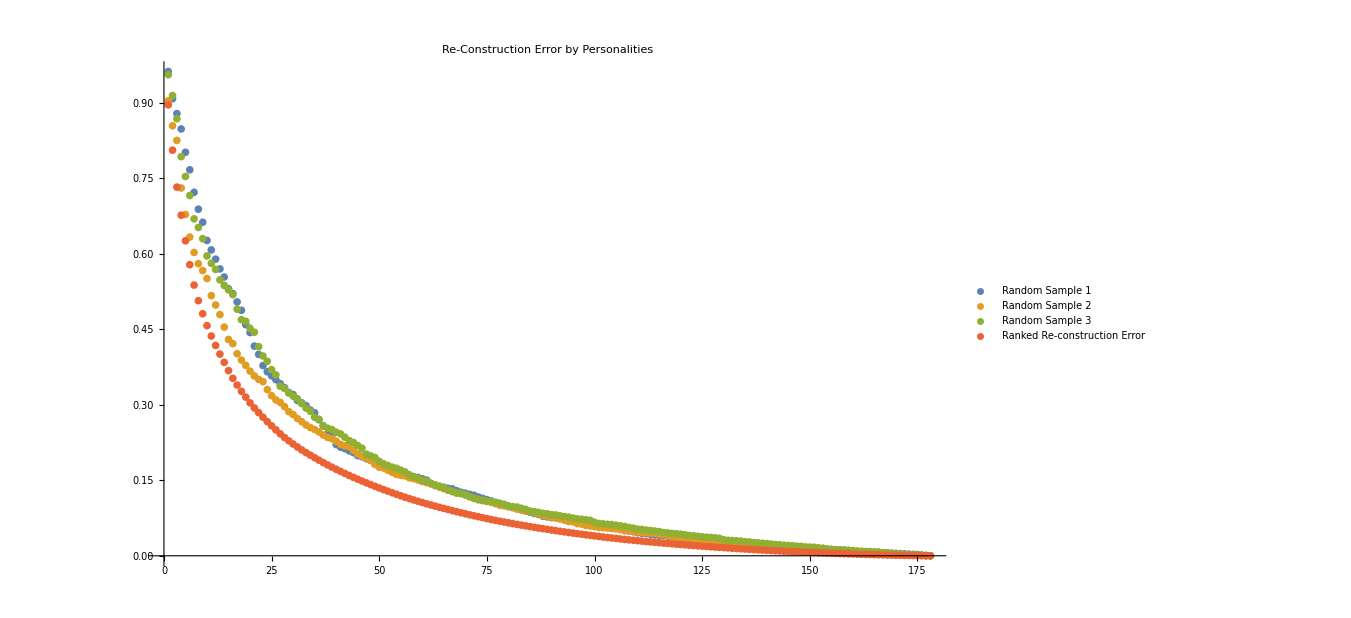

```mathematica
ListPlot[
{randomSamples[[1]],
randomSamples[[2]],
randomSamples[[3]],
Callout[#2, ""]&@@@indexedErrors
}, 
PlotLegends->{"Random Sample 1","Random Sample 2","Random Sample 3", "Ranked Re-construction Error"},
PlotLabel->"Re-Construction Error by Personalities",
ImageSize->1000,
PlotRange->All]
```

```mathematica
indexedErrors=;
```

## Top PCA Reconstructed Errors

```mathematica
ClearAll[reconstructErrorPersonalities,reconstructErrorGivenBasis];

reconstructErrorGivenBasis[basisVectors_]:=Block[{projected,reconstructed},projected=standardized.Transpose[Orthogonalize[basisVectors]];
reconstructed=projected.Orthogonalize[basisVectors];
Mean[Total[(standardized-reconstructed)^2,{2}]]]

reconstructErrorPersonalities[persIndices_]:=reconstructErrorPersonalities[persIndices]=Block[{basisVectors},basisVectors=standardized[[persIndices]];
reconstructErrorGivenBasis[basisVectors]]

PCAErrorSummary[standardized_,personalityNames_,numComponents_]:=Block[{eigenvectors,cosineDistances,closestPoints,combinedDistances,closestPCADistances},eigenvectors=Transpose[PrincipalComponents[Transpose[standardized]]];
cosineDistances=Table[CosineDistance[eigenvectors[[i]],#]&/@standardized,{i,numComponents}];
closestPoints=Table[Ordering[cosineDistances[[i]],3],{i,numComponents}];
combinedDistances=Table[CosineDistance[Total[standardized[[closestPoints[[i]]]]],eigenvectors[[i]]],{i,numComponents}];
closestPCADistances=Table[closestPoints[[i]],{i,numComponents}];
{closestPCADistances,combinedDistances}]
```

```mathematica
PCAErrorSummary[standardized_,personalityNames_,numComponents_]:=Block[{eigenvectors,cosineDistances,closestIndices,combinedDistances},eigenvectors=Transpose[PrincipalComponents[Transpose[standardized]]];
cosineDistances=Table[CosineDistance[eigenvectors[[i]],#]&/@standardized,{i,numComponents}];
closestIndices=Table[Ordering[cosineDistances[[i]],1][[1]],{i,numComponents}];
combinedDistances=Table[With[{closestThreeIndices=Ordering[cosineDistances[[i]],3]},CosineDistance[Total[standardized[[closestThreeIndices]]],eigenvectors[[i]]]],{i,numComponents}];
{closestIndices,combinedDistances}]
```

```mathematica
PCAErrorSummary[standardized_,personalityNames_,numComponents_]:=Block[{eigenvectors,cosineDistances,closestPoints,combinedDistances,closestPCADistances},eigenvectors=Transpose[PrincipalComponents[Transpose[standardized]]];
cosineDistances=Table[CosineDistance[eigenvectors[[i]],#]&/@standardized,{i,numComponents}];
closestPoints=Table[Ordering[cosineDistances[[i]],3],{i,numComponents}];
combinedDistances=Table[CosineDistance[Total[standardized[[closestPoints[[i]]]]],eigenvectors[[i]]],{i,numComponents}];
closestPCADistances=Table[Total[cosineDistances[[i,closestPoints[[i]]]]],{i,numComponents}];
{closestPCADistances,combinedDistances}]
```

```mathematica
numComponents=178;

{closestPCADistances,combinedPCADistances}=PCAErrorSummary[standardized,personalityNames,numComponents];

PCAErrors=reconstructErrorPersonalities[Flatten[closestPCADistances[[;;#]]]]&/@Range[Length[closestPCADistances]];
```

```mathematica
(*Create a list of {index,error} pairs*)
indexedErrorsPCA=Thread[{closestPCADistances,PCAErrors}];
```

```mathematica
(*Sort the pairs by error (ascending order)*)
sortedIndexedErrors=SortBy[indexedErrorsPCA,Last];
ListPlot[
{randomSamples[[1]],
randomSamples[[2]],
randomSamples[[3]],
Callout[#2, personalityNames[[#1]]]&@@@indexedErrorsPCA
}, 
PlotLegends->{"Top PCA Ranked Re-construction Error","Random Sample 1","Random Sample 2","Random Sample 3"},
PlotLabel->"Re-Construction Error by Closest PCA Personalities",
ImageSize->1000,
PlotRange->All]
```

-Graphics-

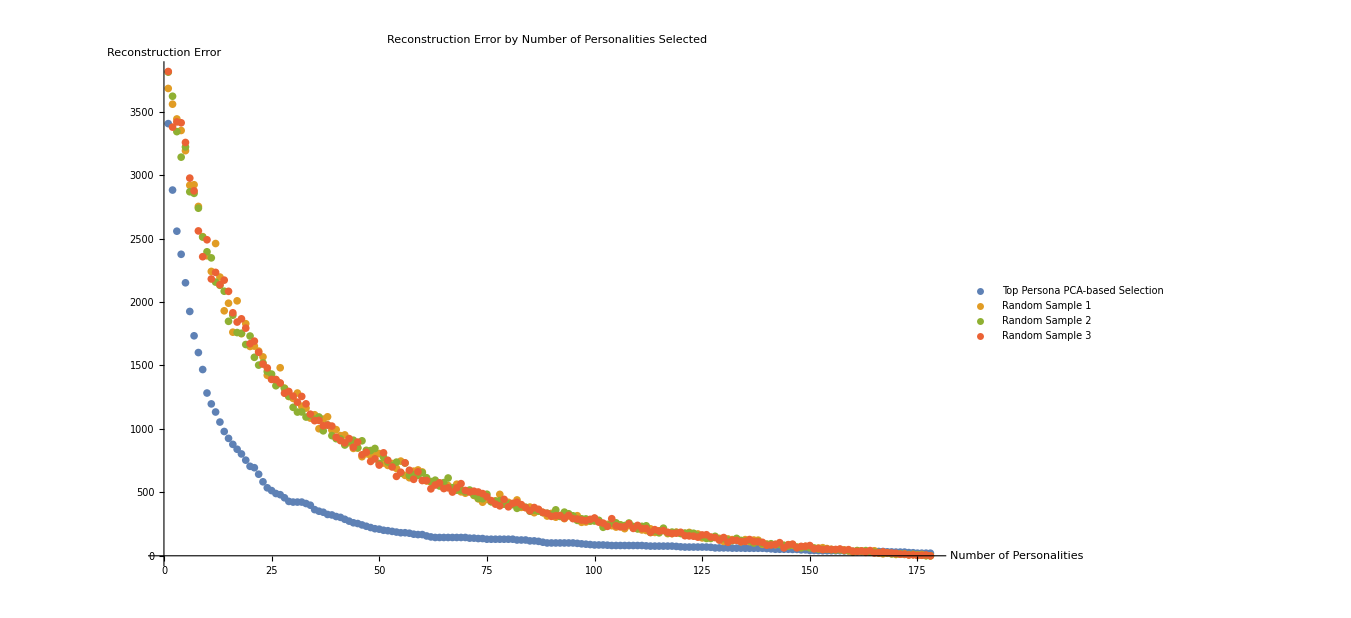

```mathematica
(*Previous functions remain the same*)(*Calculate PCA Errors*)PCAErrors=reconstructErrorPersonalities[Flatten[closestPCADistances[[;;#]]]]&/@Range[Length[closestPCADistances]];

(*Create a list of {index,error} pairs*)
indexedErrorsPCA=Thread[{Range[Length[PCAErrors]],PCAErrors}];

(*Calculate errors for random samples*)
randomSampleErrors=Table[reconstructErrorPersonalities[RandomSample[Range[Length[standardized]],#]]&/@Range[Length[closestPCADistances]],{3}];

(*Plotting*)
ListPlot[{Callout[#2,Row[{#1,": ",personalityNames[[Flatten[closestPCADistances[[;;#1]]]]]}]]&@@@indexedErrorsPCA,randomSampleErrors[[1]],randomSampleErrors[[2]],randomSampleErrors[[3]]},PlotLegends->{"Top Persona PCA-based Selection","Random Sample 1","Random Sample 2","Random Sample 3"},PlotLabel->"Reconstruction Error by Number of Personalities Selected",AxesLabel->{"Number of Personalities","Reconstruction Error"},ImageSize->1000,PlotRange->All]
```